-0.825

0.766485

-0.75

2.93382

2.96452

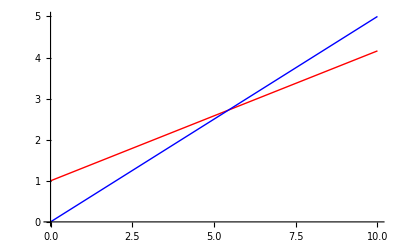

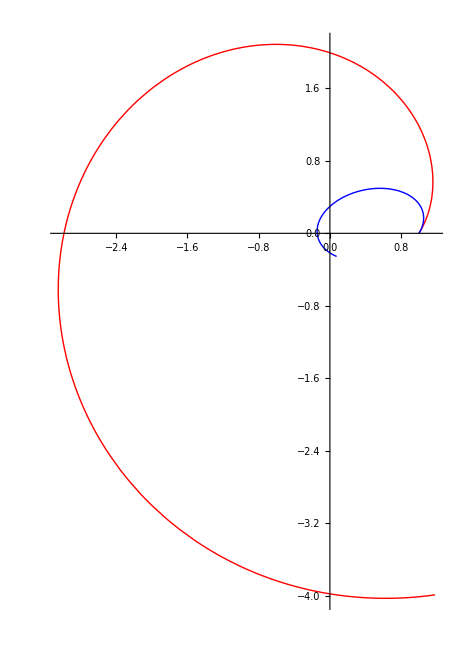

```mathematica
r0=1;
L0=0.5;
M0=1;
dE0=0.05;
a=-1;
b=0;
U[r_,a_,b_]=a*Exp[-b*r]/r;
E0=N[U[r0,a,b]+L0^2/(2*M0*r0^2)+dE0]
tmax=10;
p2=-L0^2/a/M0;
e=N[Sqrt[2*E0*L0^2/a^2/M0 + 1]]
p2/r0-1
phi0=ArcCos[(p2/r0-1)/e]
T=Pi*p2*p2/L0*2*M0/(1-e*e)^(3/2)
s=NDSolve[{r'[t]==Sqrt[2/M0]*Sqrt[E0-U[r[t],a,b]-L0^2/(2*M0*(r[t])^2)],p'[t]==L0/(M0*(r[t])^2),r[0]==r0,p[0]==0},{r,p},{t,0,tmax},Method->"Projection"];
Plot[Evaluate[{r[t],p[t]}/.s],{t,0,tmax},PlotRange->All, PlotStyle->{Red,Blue},PlotRange->All]
ParametricPlot[{Evaluate[{r[t]*Cos[p[t]],r[t]*Sin[p[t]]}/.s],Evaluate[{p2/(1+e*Cos[p[t]+phi0])*Cos[p[t]], p2/(1+e*Cos[p[t]+phi0])*Sin[p[t]]}/.s]},{t,0,tmax},PlotRange->All,PlotStyle->{Red, Blue}]
```